```mathematica
fib[n_]:=fib[n-1]+fib[n-2];
fib[1]=1;
fib[0]=1;
```

```mathematica
Array[fib,8]
```

{1,2,3,5,8,13,21,34}

```mathematica
21/34//N
```

0.617647

```mathematica
t=Table[Timing[fib[n]][[1]],{n,1,30}]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.004,0.004,0.004,0.008,0.016,0.024,0.02,0.036,0.052,0.092,0.148,0.24,0.384,0.608,1.008,1.632}

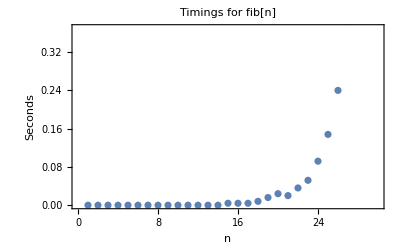

```mathematica
ListPlot[t,PlotLabel->"Timings for fib[n]",Frame->True,FrameLabel->{"n","Seconds"},FrameTicks->{Range[0,30,2],Automatic}]
```

```mathematica
Trace[fib[4],fib[_]]
```

{fib[4],{fib[3],{fib[2],{fib[1]},{fib[0]}},{fib[1]}},{fib[2],{fib[1]},{fib[0]}}}

```mathematica
Trace[fib[4]]//TableForm
```

fib[4] |  |  |  |  |  | 
fib[4-1]+fib[4-2] |  |  |  |  |  | 
4-1
3 | fib[3] | fib[3-1]+fib[3-2] | 3-1 | 2 | 
fib[2] |  | 
fib[2-1]+fib[2-2] |  | 
2-1
1 | fib[1] | 1
2-2
0 | fib[0] | 1
1+1 |  | 
2 |  |  | 3-2 | 1
fib[1] | 
1 |  | 2+1 | 3
4-2
2 | fib[2] | fib[2-1]+fib[2-2] | 2-1 | 1
fib[1] | 
1 |  | 2-2 | 0
fib[0] | 
1 |  | 1+1 | 2
3+2 |  |  |  |  |  | 
5 |  |  |  |  |  |

```mathematica
Table[Count[Flatten[Trace[fib[i],fib[_]]],HoldForm[fib[1]]],{i,1,12}]
```

{1,1,2,3,5,8,13,21,34,55,89,144}

One way to solve this problem efficiently is to perform the computation “bottom up”

```mathematica
bufib[n_]:=Nest[{#[[2]],Plus@@#}&,{0,1},n][[2]];(*保存了上次的最终结果*)
```

```mathematica
Table[bufib[n],{n,0,11}]
```

{1,1,2,3,5,8,13,21,34,55,89,144}

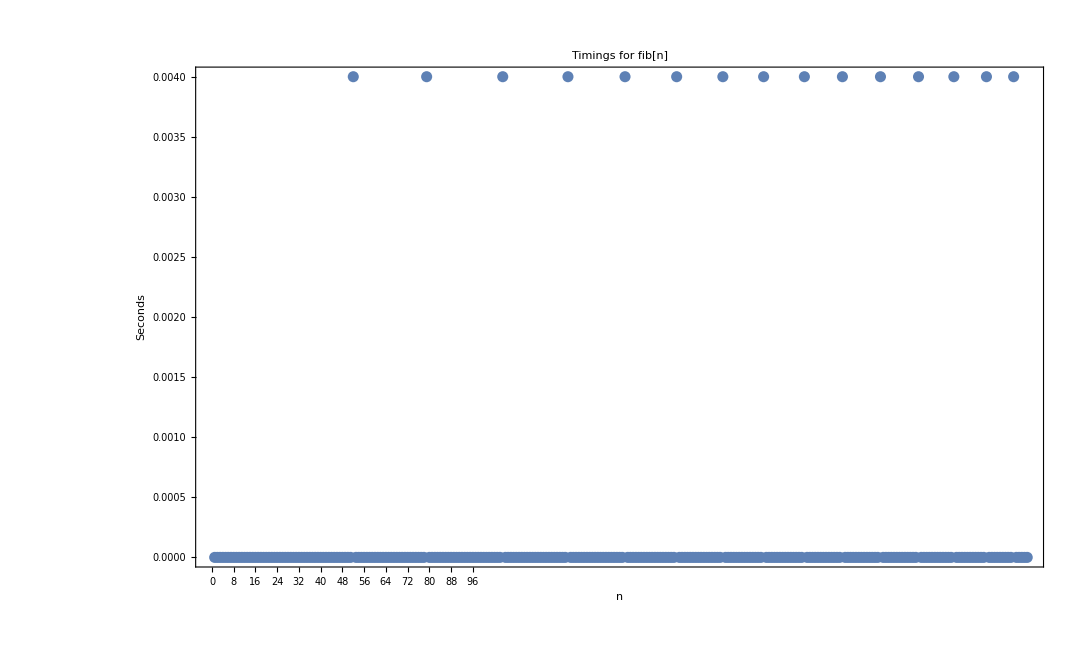

```mathematica
t=Table[Timing[bufib[n]][[1]],{n,1,300}];
ListPlot[t,PlotLabel->"Timings for fib[n]",Frame->True,FrameLabel->{"n","Seconds"},FrameTicks->{Range[0,300,2],Automatic}]
```

#### A more general and elegant solution, which is the topic of the present section, is to cache the results of earlier computations.

```mathematica
Clear[fib]
fib[n_]:=fib[n]=fib[n-1]+fib[n-2];(*the defination of the function is dynamic.*)
fib[0]=fib[1]=1;
```

```mathematica
?fib
```

Global`fib

fib[0]=1
 
fib[1]=1
 
fib[n_]:=fib[n]=fib[n-1]+fib[n-2]

```mathematica
fib[3]
```

3

```mathematica
?fib
```

Global`fib

fib[0]=1
 
fib[1]=1
 
fib[2]=2
 
fib[3]=3
 
fib[n_]:=fib[n]=fib[n-1]+fib[n-2]

```mathematica
Timing[fib[16]]
```

{0.,1597}

```mathematica
Timing[fib[100]]
```

{0.,573147844013817084101}

```mathematica
?fib
```

Global`fib

fib[0]=1
 
fib[1]=1
 
fib[2]=2
 
fib[3]=3
 
fib[4]=5
 
fib[5]=8
 
fib[6]=13
 
fib[7]=21
 
fib[8]=34
 
fib[9]=55
 
fib[10]=89
 
fib[11]=144
 
fib[12]=233
 
fib[13]=377
 
fib[14]=610
 
fib[15]=987
 
fib[16]=1597
 
fib[17]=2584
 
fib[18]=4181
 
fib[19]=6765
 
fib[20]=10946
 
fib[21]=17711
 
fib[22]=28657
 
fib[23]=46368
 
fib[24]=75025
 
fib[25]=121393
 
fib[26]=196418
 
fib[27]=317811
 
fib[28]=514229
 
fib[29]=832040
 
fib[30]=1346269
 
fib[31]=2178309
 
fib[32]=3524578
 
fib[33]=5702887
 
fib[34]=9227465
 
fib[35]=14930352
 
fib[36]=24157817
 
fib[37]=39088169
 
fib[38]=63245986
 
fib[39]=102334155
 
fib[40]=165580141
 
fib[41]=267914296
 
fib[42]=433494437
 
fib[43]=701408733
 
fib[44]=1134903170
 
fib[45]=1836311903
 
fib[46]=2971215073
 
fib[47]=4807526976
 
fib[48]=7778742049
 
fib[49]=12586269025
 
fib[50]=20365011074
 
fib[51]=32951280099
 
fib[52]=53316291173
 
fib[53]=86267571272
 
fib[54]=139583862445
 
fib[55]=225851433717
 
fib[56]=365435296162
 
fib[57]=591286729879
 
fib[58]=956722026041
 
fib[59]=1548008755920
 
fib[60]=2504730781961
 
fib[61]=4052739537881
 
fib[62]=6557470319842
 
fib[63]=10610209857723
 
fib[64]=17167680177565
 
fib[65]=27777890035288
 
fib[66]=44945570212853
 
fib[67]=72723460248141
 
fib[68]=117669030460994
 
fib[69]=190392490709135
 
fib[70]=308061521170129
 
fib[71]=498454011879264
 
fib[72]=806515533049393
 
fib[73]=1304969544928657
 
fib[74]=2111485077978050
 
fib[75]=3416454622906707
 
fib[76]=5527939700884757
 
fib[77]=8944394323791464
 
fib[78]=14472334024676221
 
fib[79]=23416728348467685
 
fib[80]=37889062373143906
 
fib[81]=61305790721611591
 
fib[82]=99194853094755497
 
fib[83]=160500643816367088
 
fib[84]=259695496911122585
 
fib[85]=420196140727489673
 
fib[86]=679891637638612258
 
fib[87]=1100087778366101931
 
fib[88]=1779979416004714189
 
fib[89]=2880067194370816120
 
fib[90]=4660046610375530309
 
fib[91]=7540113804746346429
 
fib[92]=12200160415121876738
 
fib[93]=19740274219868223167
 
fib[94]=31940434634990099905
 
fib[95]=51680708854858323072
 
fib[96]=83621143489848422977
 
fib[97]=135301852344706746049
 
fib[98]=218922995834555169026
 
fib[99]=354224848179261915075
 
fib[100]=573147844013817084101
 
fib[n_]:=fib[n]=fib[n-1]+fib[n-2]

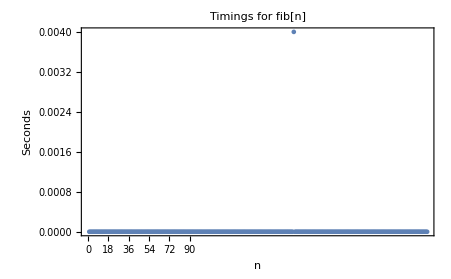

```mathematica
t=Table[Timing[fib[n]][[1]],{n,1,300}];
ListPlot[t,PlotLabel->"Timings for fib[n]",Frame->True,FrameLabel->{"n","Seconds"},FrameTicks->{Range[0,300,2],Automatic}]
```